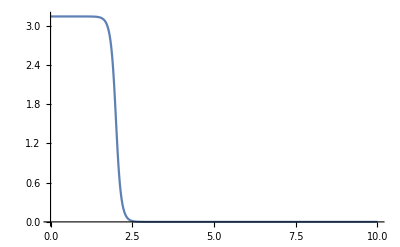

```mathematica
Clear[Θ,R,w,m,γ]
R=2;w=.1;m=1;γ=π;
Θ[r_]:=If[r==0,π,2ArcTan[Sinh[R/w]/Sinh[r/w]]];
Plot[Θ[r],{r,0,10}]
```

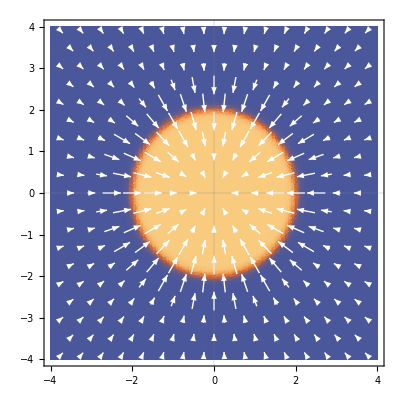

```mathematica
Clear[S,Φ,x,y]
ϕ[x_,y_]:=Arg[x+ⅈ y]
Φ[ϕ_]:=m ϕ+γ
S[r_,ϕ_]:={Sin[Θ[r]]Cos[Φ[ϕ]],Sin[Θ[r]]Sin[Φ[ϕ]],-Cos[Θ[r]]} 
Show[DensityPlot[S[√(x^2+y^2),ϕ[x,y]][[3]],{x,-2R,2R},{y,-2R,2R},MaxRecursion->2,PlotPoints->100,PlotTheme->"Scientific"],VectorPlot[S[√(x^2+y^2),ϕ[x,y]][[{1,2}]],{x,-2R,2R},{y,-2R,2R},VectorScaling->Automatic,VectorSizes->Automatic,VectorStyle->White,VectorColorFunction->None]]
```

```mathematica
(* Discretize the field *)
L1=8;
L2=8;
a1={1.,0,0};
a2=1/2{1,√3,0}//N;
latt =Flatten[Table[a1*l1+a2*l2,{l1,-L1,L1},{l2,-L2,L2}],1];
Ss = Table[S[√(v[[1]]^2+v[[2]]^2),ϕ[v[[1]],v[[2]]]],{v,latt}];
```

```mathematica
Graphics3D[{Point[{#[[1,1]],#[[1,2]],0}],Cone[{{#[[1,1]],#[[1,2]],0}-0.25#[[2]],{#[[1,1]],#[[1,2]],0}+0.25#[[2]]},0.4]}&/@({latt,Ss}ᵀ),ImageSize->800,ViewPoint->Top];
Show[%,Graphics3D[Text[#,latt[[#]]]&/@Range[Length[latt]]]]
dist[n1_,n2_]:=Norm[n2-n1];
dists=Outer[dist,latt,latt,1];
ddists=DeleteDuplicates[Chop[dists//Flatten]]//Sort;
(*neighbors={#,#}&/@latt[[All,1]];*)
neighbors=First[Position[dists,x_/;Abs[x-#]<1*^-8,3]&/@ddists[[{2,1}]]];//AbsoluteTiming;
nnPlot=Graphics3D[{{Black,CapForm["Butt"],Tube[{latt[[#[[1]]]],latt[[#[[2]]]]},0.1]}&/@neighbors},ViewPoint->Top];

triangle[s1_,s2_]:=If[Length[cs=Intersection[s1,s2]]==1&&dist[latt[[s1[[1]]]],latt[[s2[[1]]]]]<=1.&&dist[latt[[s1[[2]]]],latt[[s2[[1]]]]]<=1.&&dist[latt[[s1[[2]]]],latt[[s2[[2]]]]]<=1.&&dist[latt[[s1[[1]]]],latt[[s2[[2]]]]]<=1.,{First[cs],First[Complement[s1,s2]],First[Complement[s2,s1]]},Nothing]

triangles=DeleteDuplicates[Flatten[Outer[triangle,neighbors,neighbors,1],1]];
(triangles//Length)/6
Clear[X,i1,i2,i3]
X[i1_,i2_,i3_]:=1+Ss[[i1]].Ss[[i2]]+Ss[[i2]].Ss[[i3]] + Ss[[i3]].Ss[[i1]]
Y[i1_,i2_,i3_]:=Ss[[i1]].(Ss[[i2]]×Ss[[i3]])
signY[i1_,i2_,i3_]:=Ss[[i1]].(Ss[[i2]]×Ss[[i3]])*Sign[((latt[[i2]]-latt[[i1]])×(latt[[i3]]-latt[[i2]]))[[3]]]
A[i1_,i2_,i3_]:=2Arg[X[i1,i2,i3]+ⅈ Y[i1,i2,i3]]*Sign[((latt[[i2]]-latt[[i1]])×(latt[[i3]]-latt[[i2]]))[[3]]]
(* topological charge for the spin profile *)
topoDensity=Total[signY[Sequence@@#]&/@triangles]/6/4/π
topoCharge=Total[A[Sequence@@#]&/@triangles]/6/4/π
```

-Graphics3D-

512

0.132438

1.

```mathematica
(* some other magnetic profiles *)
data=ImportString["1,0.0,0.0,0.0,7.875297636239509e-14,-7.524363077049401e-17,0.03613238981796289
1,0.5,0.8660254037844386,0.0,-0.04210934218888706,-0.07293552014458315,0.034339069245345064
1,-0.5,0.8660254037844386,0.0,0.04210934218903737,-0.07293552014458375,0.034339069245344835
1,-1.0,0.0,0.0,0.08421868437800141,-2.42861286636753e-17,0.034339069245343676
1,-0.5,-0.8660254037844386,0.0,0.04210934218903786,0.07293552014458332,0.034339069245344384
1,0.5,-0.8660254037844386,0.0,-0.04210934218888637,0.07293552014458404,0.03433906924534475
1,1.0,0.0,0.0,-0.08421868437784932,9.454242944073599e-17,0.0343390692453448
1,1.5,0.8660254037844386,0.0,-0.12248334234474789,-0.07071579067402603,0.006379241070127176
1,1.0,1.7320508075688772,0.0,-0.07821234686070697,-0.13546775854206203,-0.013557465937881437
1,0.0,1.7320508075688772,0.0,7.0606714919208e-14,-0.14143158134805167,0.006379241070117636
1,-1.0,1.7320508075688772,0.0,0.07821234686084645,-0.1354677585420611,-0.01355746593789646
1,-1.5,0.8660254037844386,0.0,0.12248334234489232,-0.07071579067402711,0.0063792410701074284
1,-2.0,0.0,0.0,0.15642469372161932,4.7704895589362195e-18,-0.013557465937904732
1,-1.5,-0.8660254037844386,0.0,0.12248334234489366,0.07071579067402581,0.006379241070107422
1,-1.0,-1.7320508075688772,0.0,0.07821234686084633,0.1354677585420606,-0.013557465937896971
1,0.0,-1.7320508075688772,0.0,7.192857420790233e-14,0.1414315813480546,0.006379241070117709
1,1.0,-1.7320508075688772,0.0,-0.07821234686070506,0.1354677585420614,-0.013557465937880226
1,1.5,-0.8660254037844386,0.0,-0.12248334234475182,0.07071579067402566,0.006379241070126426
1,2.0,0.0,0.0,-0.15642469372148,2.2898349882893854e-16,-0.013557465937876656"];
latt={data[[;;,2]],data[[;;,3]],data[[;;,4]]}ᵀ;
Ss =Normalize[#]&/@({data[[;;,5]],data[[;;,6]],data[[;;,7]]}ᵀ);
```

```mathematica
data=ImportString["1,0.0,0.0,0.0,4.7383971746306486e-15,7.43572954944871e-15,0.4980530404927753
1,0.5,0.8660254037844386,0.0,-0.21208817991009032,-0.3673475032890896,0.23793206792088128
1,-0.5,0.8660254037844386,0.0,0.2120881799100971,-0.3673475032890919,0.23793206792087052
1,-1.0,0.0,0.0,0.4241763598201862,2.539323460705456e-15,0.23793206792086977
1,-0.5,-0.8660254037844386,0.0,0.21208817991009996,0.3673475032890975,0.23793206792086521
1,0.5,-0.8660254037844386,0.0,-0.2120881799100991,0.3673475032890979,0.23793206792086552
1,1.0,0.0,0.0,-0.4241763598201874,8.827682508594226e-15,0.23793206792086535
1,1.5,0.8660254037844386,0.0,-0.4209847353817898,-0.24305565029740855,0.016027813783492523
1,1.0,1.7320508075688772,0.0,-0.24210469095107362,-0.41933762547802894,-0.0634381365879438
1,0.0,1.7320508075688772,0.0,3.0589680094506022e-15,-0.4861113005948047,0.016027813783486562
1,-1.0,1.7320508075688772,0.0,0.2421046909510761,-0.4193376254780368,-0.06343813658794592
1,-1.5,0.8660254037844386,0.0,0.4209847353818004,-0.24305565029739695,0.016027813783486562
1,-2.0,0.0,0.0,0.48420938190214596,9.905338810463349e-16,-0.06343813658794624
1,-1.5,-0.8660254037844386,0.0,0.4209847353818039,0.24305565029740622,0.016027813783486666
1,-1.0,-1.7320508075688772,0.0,0.24210469095106885,0.41933762547803854,-0.0634381365879449
1,0.0,-1.7320508075688772,0.0,-6.191878607064716e-16,0.4861113005948047,0.016027813783486305
1,1.0,-1.7320508075688772,0.0,-0.24210469095107517,0.4193376254780332,-0.0634381365879482
1,1.5,-0.8660254037844386,0.0,-0.4209847353818017,0.2430556502974059,0.016027813783481316
1,2.0,0.0,0.0,-0.484209381902151,5.086371861889871e-15,-0.06343813658794048"];
latt={data[[;;,2]],data[[;;,3]],data[[;;,4]]}ᵀ;
Ss =Normalize[#]&/@({data[[;;,5]],data[[;;,6]],data[[;;,7]]}ᵀ);
```

```mathematica
data=ImportString["1,0.0,0.0,0.0,6.372506689000801e-15,-3.4949257030070235e-16,0.49805304049278604
1,0.5,0.8660254037844386,0.0,-0.212088179910085,-0.3673475032890904,0.2379320679208645
1,-0.5,0.8660254037844386,0.0,0.21208817991009676,-0.3673475032890743,0.23793206792085667
1,-1.0,0.0,0.0,0.4241763598201812,-4.1819033045481513e-16,0.23793206792085209
1,-0.5,-0.8660254037844386,0.0,0.21208817991009257,0.3673475032890841,0.23793206792085556
1,0.5,-0.8660254037844386,0.0,-0.21208817991008788,0.3673475032890725,0.2379320679208631
1,1.0,0.0,0.0,-0.4241763598201702,1.2284010614260765e-16,0.23793206792086202
1,1.5,0.8660254037844386,0.0,-0.4209847353817925,-0.24305565029739323,0.016027813783487353
1,1.0,1.7320508075688772,0.0,-0.2421046909510631,-0.4193376254780036,-0.06343813658794292
1,0.0,1.7320508075688772,0.0,2.471330431963459e-15,-0.48611130059479835,0.01602781378348675
1,-1.0,1.7320508075688772,0.0,0.24210469095106812,-0.41933762547801723,-0.06343813658794499
1,-1.5,0.8660254037844386,0.0,0.42098473538179504,-0.2430556502973975,0.016027813783485455
1,-2.0,0.0,0.0,0.48420938190212925,-2.1120427726607077e-16,-0.06343813658794589
1,-1.5,-0.8660254037844386,0.0,0.42098473538179737,0.24305565029739354,0.016027813783485674
1,-1.0,-1.7320508075688772,0.0,0.24210469095105983,0.41933762547799946,-0.06343813658794527
1,0.0,-1.7320508075688772,0.0,2.1754516590921646e-15,0.4861113005947818,0.01602781378348679
1,1.0,-1.7320508075688772,0.0,-0.24210469095106255,0.4193376254780081,-0.06343813658794317
1,1.5,-0.8660254037844386,0.0,-0.4209847353817844,0.2430556502974044,0.01602781378348673
1,2.0,0.0,0.0,-0.4842093819021197,2.3787395664331967e-16,-0.06343813658795733
1,-3.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,-3.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,-4.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,-4.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,-4.0,1.7320508075688774,0.0,0.0,0.0,-1.0
1,-3.0,1.7320508075688774,0.0,0.0,0.0,-1.0
1,-2.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,-2.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,-2.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,-3.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,-4.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,-5.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,-5.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,-5.0,1.7320508075688774,0.0,0.0,0.0,-1.0
1,-4.5,0.8660254037844388,0.0,0.0,0.0,-1.0
1,-3.5,0.8660254037844388,0.0,0.0,0.0,-1.0
1,-2.5,0.8660254037844388,0.0,0.0,0.0,-1.0
1,-2.0,1.7320508075688774,0.0,0.0,0.0,-1.0
1,-1.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,-4.0,-1.7320508075688772,0.0,0.0,0.0,-1.0
1,-3.5,-0.8660254037844386,0.0,0.0,0.0,-1.0
1,-4.5,-0.8660254037844386,0.0,0.0,0.0,-1.0
1,-5.0,-1.7320508075688772,0.0,0.0,0.0,-1.0
1,-4.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,-3.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,-3.0,-1.7320508075688772,0.0,0.0,0.0,-1.0
1,-2.5,-0.8660254037844386,0.0,0.0,0.0,-1.0
1,-3.0,0.0,0.0,0.0,0.0,-1.0
1,-4.0,0.0,0.0,0.0,0.0,-1.0
1,-5.0,0.0,0.0,0.0,0.0,-1.0
1,-5.5,-0.8660254037844386,0.0,0.0,0.0,-1.0
1,-6.0,-1.7320508075688772,0.0,0.0,0.0,-1.0
1,-5.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,-5.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-4.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-3.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-2.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,-2.0,-1.7320508075688772,0.0,0.0,0.0,-1.0
1,-0.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,0.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-1.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-1.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,-1.0,-5.196152422706631,0.0,0.0,0.0,-1.0
1,0.0,-5.196152422706631,0.0,0.0,0.0,-1.0
1,0.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,1.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,0.5,-2.5980762113533156,0.0,0.0,0.0,-1.0
1,-0.5,-2.5980762113533156,0.0,0.0,0.0,-1.0
1,-1.5,-2.5980762113533156,0.0,0.0,0.0,-1.0
1,-2.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-2.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,-2.0,-5.196152422706631,0.0,0.0,0.0,-1.0
1,-1.5,-6.0621778264910695,0.0,0.0,0.0,-1.0
1,-0.5,-6.0621778264910695,0.0,0.0,0.0,-1.0
1,0.5,-6.0621778264910695,0.0,0.0,0.0,-1.0
1,1.0,-5.196152422706631,0.0,0.0,0.0,-1.0
1,1.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,3.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,4.0,-1.7320508075688774,0.0,0.0,0.0,-1.0
1,3.0,-1.7320508075688774,0.0,0.0,0.0,-1.0
1,2.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,3.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,4.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,4.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,5.0,-1.7320508075688774,0.0,0.0,0.0,-1.0
1,4.5,-0.8660254037844388,0.0,0.0,0.0,-1.0
1,3.5,-0.8660254037844388,0.0,0.0,0.0,-1.0
1,2.5,-0.8660254037844388,0.0,0.0,0.0,-1.0
1,2.0,-1.7320508075688774,0.0,0.0,0.0,-1.0
1,1.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,2.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,2.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,3.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,4.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,5.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,5.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,4.0,1.7320508075688772,0.0,0.0,0.0,-1.0
1,4.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,3.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,3.0,1.7320508075688772,0.0,0.0,0.0,-1.0
1,3.5,0.8660254037844386,0.0,0.0,0.0,-1.0
1,4.5,0.8660254037844386,0.0,0.0,0.0,-1.0
1,5.0,1.7320508075688772,0.0,0.0,0.0,-1.0
1,5.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,5.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,4.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,3.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,2.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,2.0,1.7320508075688772,0.0,0.0,0.0,-1.0
1,2.5,0.8660254037844386,0.0,0.0,0.0,-1.0
1,3.0,0.0,0.0,0.0,0.0,-1.0
1,4.0,0.0,0.0,0.0,0.0,-1.0
1,5.0,0.0,0.0,0.0,0.0,-1.0
1,5.5,0.8660254037844386,0.0,0.0,0.0,-1.0
1,6.0,1.7320508075688772,0.0,0.0,0.0,-1.0
1,0.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,1.0,5.196152422706631,0.0,0.0,0.0,-1.0
1,0.0,5.196152422706631,0.0,0.0,0.0,-1.0
1,-0.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,0.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,1.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,1.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,2.0,5.196152422706631,0.0,0.0,0.0,-1.0
1,1.5,6.0621778264910695,0.0,0.0,0.0,-1.0
1,0.5,6.0621778264910695,0.0,0.0,0.0,-1.0
1,-0.5,6.0621778264910695,0.0,0.0,0.0,-1.0
1,-1.0,5.196152422706631,0.0,0.0,0.0,-1.0
1,-1.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,-1.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,-0.5,2.5980762113533156,0.0,0.0,0.0,-1.0
1,0.5,2.5980762113533156,0.0,0.0,0.0,-1.0
1,1.5,2.5980762113533156,0.0,0.0,0.0,-1.0
1,2.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,2.5,4.330127018922193,0.0,0.0,0.0,-1.0"];
latt={data[[;;,2]],data[[;;,3]],data[[;;,4]]}ᵀ;
Ss =Normalize[#]&/@({data[[;;,5]],data[[;;,6]],data[[;;,7]]}ᵀ);
Ss =#&/@({data[[;;,5]],data[[;;,6]],data[[;;,7]]}ᵀ);
```